# Truc 1

## Chapitre 1

```mathematica
Plot[x*Exp[-x] + 2, {x, -10, 10}]
```

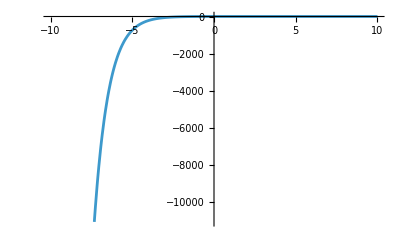

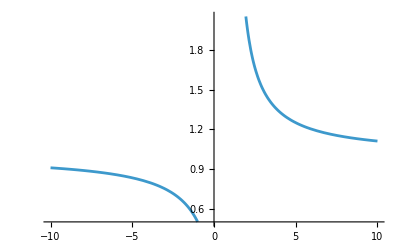

```mathematica
f[x_] := Sum[1/(x^i), {i, 0, Infinity}]
Plot[f[x], {x, -10, 10}]
```

```mathematica
WebSearch["Surface France"]
```

```mathematica
1 cm 3 = 35 grains de riz
```

```mathematica
(2^64 - 1) / 35
```

3689348814741910323/7

```mathematica
3689348814741910323/7/(551500 *10^10)
```

```mathematica
3689348814741910323/38605000000000000// N
```

95.5666

```mathematica
UnitConvert[(Quantity[(2^64 - 1)/35., "Centimeters"^3]/CountryData["China", "Area"]), "Centimeters"]
```

5.49184 cm

```mathematica
Column[
Table[
Expand[(a + b)^i], 
{i, 0, 10}
], Background->{{LightBlue, LightRed}}, FontColor-> {Black}
]
```

1
a+b
a^2+2 a b+b^2
a^3+3 a^2 b+3 a b^2+b^3
a^4+4 a^3 b+6 a^2 b^2+4 a b^3+b^4
a^5+5 a^4 b+10 a^3 b^2+10 a^2 b^3+5 a b^4+b^5
a^6+6 a^5 b+15 a^4 b^2+20 a^3 b^3+15 a^2 b^4+6 a b^5+b^6
a^7+7 a^6 b+21 a^5 b^2+35 a^4 b^3+35 a^3 b^4+21 a^2 b^5+7 a b^6+b^7
a^8+8 a^7 b+28 a^6 b^2+56 a^5 b^3+70 a^4 b^4+56 a^3 b^5+28 a^2 b^6+8 a b^7+b^8
a^9+9 a^8 b+36 a^7 b^2+84 a^6 b^3+126 a^5 b^4+126 a^4 b^5+84 a^3 b^6+36 a^2 b^7+9 a b^8+b^9
a^10+10 a^9 b+45 a^8 b^2+120 a^7 b^3+210 a^6 b^4+252 a^5 b^5+210 a^4 b^6+120 a^3 b^7+45 a^2 b^8+10 a b^9+b^10

```mathematica
Table[
{couleur, symbole},
{couleur, {StandardRed, Black}},
{symbole, {"Valet", "Dame", "Roi"}}
]
```

{{{RGBColor[0.93, 0.27, 0.27],Valet},{RGBColor[0.93, 0.27, 0.27],Dame},{RGBColor[0.93, 0.27, 0.27],Roi}},{{GrayLevel[0],Valet},{GrayLevel[0],Dame},{GrayLevel[0],Roi}}}

```mathematica
Dataset[ElementData[][[2]]["Dataset"], MaxItems -> All]
```

```mathematica
Table[{ElementData[][[x]], ElementData[][[x]]["DiscoveryDate"]},
{x, 1, 118}
]
```

{{hydrogen,Year: 1766},{helium,Year: 1868},{lithium,Year: 1817},{beryllium,Year: 1797},{boron,Year: 1808},{carbon,Year: 3750 BC},{nitrogen,Year: 1772},{oxygen,Year: 1774},{fluorine,Year: 1886},{neon,Year: 1898},{sodium,Year: 1807},{magnesium,Year: 1755},{aluminum,Year: 1825},{silicon,Year: 1824},{phosphorus,Year: 1669},{sulfur,Year: 500 BC},{chlorine,Year: 1774},{argon,Year: 1894},{potassium,Year: 1807},{calcium,Year: 1807},{scandium,Year: 1879},{titanium,Year: 1791},{vanadium,Year: 1801},{chromium,Year: 1780},{manganese,Year: 1774},{iron,Year: 2000 BC},{cobalt,Year: 1735},{nickel,Year: 1751},{copper,Year: 8000 BC},{zinc,Year: 1500},{gallium,Year: 1875},{germanium,Year: 1886},{arsenic,Year: 1250},{selenium,Year: 1817},{bromine,Year: 1826},{krypton,Year: 1898},{rubidium,Year: 1861},{strontium,Year: 1790},{yttrium,Year: 1794},{zirconium,Year: 1789},{niobium,Year: 1801},{molybdenum,Year: 1781},{technetium,Year: 1937},{ruthenium,Year: 1808},{rhodium,Year: 1803},{palladium,Year: 1803},{silver,Year: 3000 BC},{cadmium,Year: 1817},{indium,Year: 1863},{tin,Year: 3000 BC},{antimony,Year: 3000 BC},{tellurium,Year: 1783},{iodine,Year: 1811},{xenon,Year: 1898},{cesium,Year: 1860},{barium,Year: 1808},{lanthanum,Year: 1839},{cerium,Year: 1803},{praseodymium,Year: 1885},{neodymium,Year: 1885},{promethium,Year: 1945},{samarium,Year: 1879},{europium,Year: 1901},{gadolinium,Year: 1880},{terbium,Year: 1843},{dysprosium,Year: 1886},{holmium,Year: 1878},{erbium,Year: 1842},{thulium,Year: 1879},{ytterbium,Year: 1878},{lutetium,Year: 1907},{hafnium,Year: 1923},{tantalum,Year: 1802},{tungsten,Year: 1783},{rhenium,Year: 1925},{osmium,Year: 1803},{iridium,Year: 1803},{platinum,Year: 1735},{gold,Year: 2500 BC},{mercury,Year: 1500 BC},{thallium,Year: 1861},{lead,Year: 4000 BC},{bismuth,Year: 1400},{polonium,Year: 1898},{astatine,Year: 1940},{radon,Year: 1900},{francium,Year: 1939},{radium,Year: 1898},{actinium,Year: 1899},{thorium,Year: 1829},{protactinium,Year: 1913},{uranium,Year: 1789},{neptunium,Year: 1940},{plutonium,Year: 1940},{americium,Year: 1944},{curium,Year: 1944},{berkelium,Year: 1949},{californium,Year: 1950},{einsteinium,Year: 1952},{fermium,Year: 1952},{mendelevium,Year: 1955},{nobelium,Year: 1958},{lawrencium,Year: 1961},{rutherfordium,Year: 1964},{dubnium,Year: 1967},{seaborgium,Year: 1967},{bohrium,Year: 1981},{hassium,Year: 1984},{meitnerium,Year: 1982},{darmstadtium,Year: 1994},{roentgenium,Year: 1994},{copernicium,Year: 1996},{nihonium,Year: 2004},{flerovium,Year: 1998},{moscovium,Year: 2004},{livermorium,Year: 2000},{tennessine,Year: 2010},{oganesson,Year: 2006}}

```mathematica
UnitConvert[PlanetData["Jupiter"]["DistanceFromSun"] / Entity["PhysicalConstant", "SpeedOfLight"]["Value"], "minutes"]
```

42.9355 min

```mathematica
SolarEclipse[]
```

Sun 21 Sep 2025 20:41:54GMT+1

```mathematica
SolarEclipse[DateObject[DateObject[{2025,9,21,20,41,54.995791450492106},"Instant","Gregorian",1.]],"EclipseMap"]
```

```mathematica
Solve[x^4 == -2, x]
```

{{x→-(-2)^(1/4)},{x→-ⅈ (-2)^(1/4)},{x→ⅈ (-2)^(1/4)},{x→(-2)^(1/4)}}

```mathematica
Solve[x+2 == 2*x, x]
```

{{x→2}}

```mathematica
Solve[Zeta[x] == 0, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-56}}

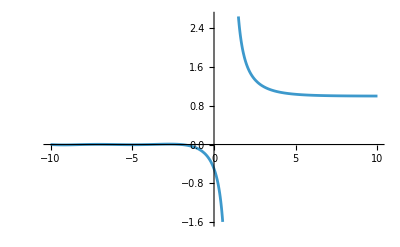

```mathematica
Plot[Zeta[x], {x, -10, 10}]
```

```mathematica
Solve[
{
3/Sqrt[1 + a^2] ==x/a, 2/Sqrt[1 + (x-a)^2] == x/(x-a)}, {x, a}, PositiveReals] // N
```

{{x→1.23119,a→0.45004}}

Power::infy: Infinite expression 1/0. encountered.

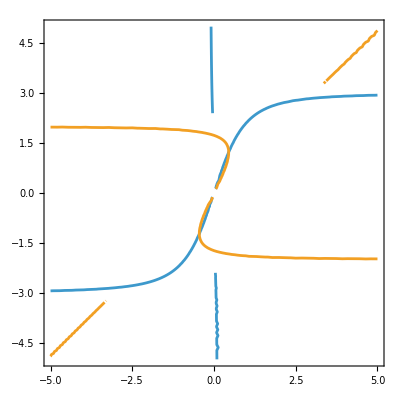

```mathematica
ContourPlot[{
3/Sqrt[1 + a^2] ==x/a, 2/Sqrt[1 + (x-a)^2] == x/(x-a)}, {a, -5, 5}, {x, -5, 5}]
```

```mathematica
Manipulate[Plot[Sin[1/(a x)],{x,-1, 1}],{a,-5,0.000001}]
```

## Chapitre 2 : Fonctions

```mathematica
f = ImageIdentify[CurrentImage[]]
```

person

```mathematica
Clear[f]
```

```mathematica
f[x_] := x*Exp[-x]+2
```

```mathematica
D[f[x], x]
```

ⅇ^-x-ⅇ^-x x

```mathematica
Solve[f'[x]==0, x]
```

{{x→1}}

```mathematica
g = 9.81
Integrate[Integrate[-g, t, GeneratedParameters->C], t, GeneratedParameters->C]
```

9.81

-4.905 t^2+t C[1]+C[2]

```mathematica
ImageRestyle[Import["https://i.kym-cdn.com/photos/images/original/000/041/494/1241026091_youve_been_rickrolled.gif"][[1]], WebImageSearch["Van Gogh"][[7]]]
```

-Graphics-

```mathematica
style_ref = WebImageSearch["Van Gogh"][[7]]
imagess = Import["https://i.kym-cdn.com/photos/images/original/000/041/494/1241026091_youve_been_rickrolled.gif"][[1]]
nouv_images = ImageRestyle[#, style_ref] &/@ imagess
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Clear[f]
```

```mathematica
f[x_] := Column[{x, CountryData[x, "Flag"], CountryData[x, "Population"], CountryData[x, "CapitalCity"]}]
```

```mathematica
f["France"]
```